```mathematica
Quit[]
```

## Input

```mathematica
<<"/home/riccardo/Programs/FeynArts/FeynArts/FeynArts.m"
```

FeynArts 3.11 (25 Mar 2022)

by Hagen Eck, Sepp Kueblbeck, and Thomas Hahn

```mathematica
<<"/home/riccardo/Programs/FormCalc/FormCalc/FormCalc.m"
```

FormCalc 9.10 (30 Aug 2022)

by Thomas Hahn

```mathematica
Remove[q1]
Remove[q2]
<<"/home/riccardo/Programs/ABISS/ABISS.m"
```

+++++ ABISS` +++++
Version 1.0.0

Amplitudes Builder, Interference Solver and Simplifier

A link to the model file SMbgf_Anglerfish.mod has been added to the FeynArts directory

A link to the model file SMbgf_FARAMIR_general_backup.mod has been added to the FeynArts directory

A link to the model file SMbgf_FARAMIR_general+SM.mod has been added to the FeynArts directory

A link to the model file SMbgfQCD_Anglerfish.mod has been added to the FeynArts directory

A link to the model file SMbgf_TelescopeOctopus_backup.mod has been added to the FeynArts directory

```mathematica
SetPath[NotebookDirectory[]];
```

Define the process:

```mathematica
SetProcess[{V[30]}->{V[30]}];
```

Generate default Input files

```mathematica
GenerateInput[];
```

Input file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WW/input/kinematics.m already exist. It will NOT be overwritten.

Input file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WW/input/integral_families.m already exist. It will NOT be overwritten.

Import the input files (kinematics + integral families).

```mathematica
ImportInput[];
```

Imported input file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WW/input/integral_families.m.

Imported input file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WW/input/kinematics.m.

## Diagrams generation

```mathematica
CKM=IndexDelta;
```

```mathematica
SetOptions[InsertFields,  Model -> "SMbgf_Anglerfish", GenericModel ->"Lorentzbgf", InsertionLevel->{Particles}, Restrictions->{NoQuarkMixing}, ExcludeParticles-> {}];
```

```mathematica
process={V[30]}->{V[30]};
```

```mathematica
topologies1L=CreateTopologies[1,1-> 1,ExcludeTopologies->Tadpoles];
```

```mathematica
fields1L=InsertFields[topologies1L, process];
```

loading generic model file /home/riccardo/Programs/FeynArts/FeynArts/Models/Lorentzbgf.gen

> $GenericMixing is OFF

generic model {Lorentzbgf} initialized

loading classes model file /home/riccardo/Programs/FeynArts/FeynArts/Models/SMbgf_Anglerfish.mod

> 60 particles (incl. antiparticles) in 24 classes

> $CounterTerms are ON

> 689 vertices

> 334 counterterms of order 1

> 2 counterterms of order 2

classes model {SMbgf_Anglerfish} initialized

Excluding 24 field point(s) (incl. charge-conjugate ones)

inserting at level(s) {Particles}

> Top. 1: 10 Particles insertions

> Top. 2: 18 Particles insertions

Restoring 24 field point(s)

in total: 28 Particles insertions

```mathematica
amp1L=CreateFeynAmp[fields1L];
```

creating amplitudes at level(s) {Particles}

> Top. 1: 10 Particles amplitudes

> Top. 2: 18 Particles amplitudes

in total: 28 Particles amplitudes

> Top. 1 ac/bc/cc.m, 0 diagrams

> Top. 2 ac/bd/cdcd.m, 0 diagrams

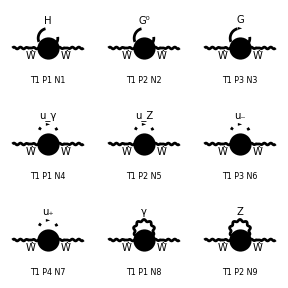

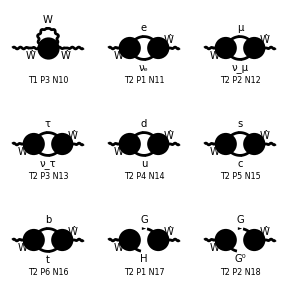

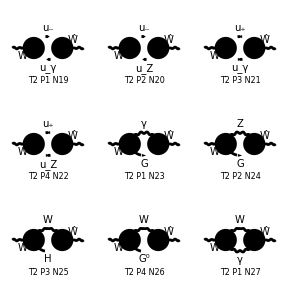

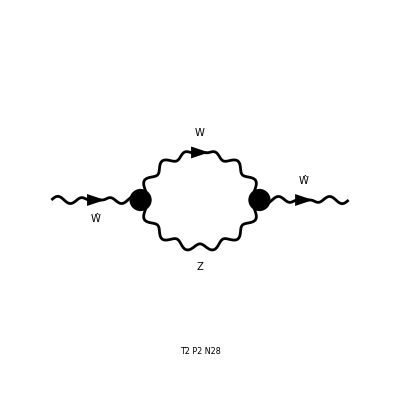

```mathematica
Paint[fields1L];
```

```mathematica
myAmp1L=ExtractAmplitude[amp1L]; (*"Extracts from a FeynArts amplitude a list of amplitudes in the format understood by ABISS."*)
```

```mathematica
SaveAmplitudes[myAmp1L,"OneLoopAmplitudes.m"];
```

Amplitudes saved in /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WW/feynArts_amplitudes/OneLoopAmplitudes.m

## Longitudinal and Transverse Part

### Projectors

```mathematica
l[Lor1_,Lor2_]:=-SP[p1,{Lor1}]SP[p1,{Lor2}]/SP[p1,p1]
```

```mathematica
t[Lor1_,Lor2_]:=(-SP[{Lor1},{Lor2}]+SP[p1,{Lor1}]SP[p1,{Lor2}]/SP[p1,p1])/(d-1)
```

### Remove polarization vectors

```mathematica
removePolarizationVectors={PolarizationVector[V[30],p_,i_]->1,Conjugate[PolarizationVector][V[30],p_,i_]->1}
```

{ep[V[30],p_,i_]→1,ep^*[V[30],p_,i_]→1}

## Interference

```mathematica
myAmp1LnoEP=myAmp1L/.removePolarizationVectors;
```

```mathematica
AmpSquare[myAmp1LnoEP[[11]]l[Lor1,Lor2],1]
```

1/(8 π^4 psq)ⅈ EL^2 gWlN gWNl KiraPropagator[q1,0] KiraPropagator[-p1+q1,ME] (psq SP[p1,q1]-2 SP[p1,q1]^2+psq SP[q1,q1])

```mathematica
SquareSimplifyAndSave[myAmp1LnoEP*l[Lor1,Lor2],{1}]
```

Computed contribution 1-1.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WW//interferences/Contribution_1_1.m.

Computed contribution 2-1.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WW//interferences/Contribution_2_1.m.

Computed contribution 3-1.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WW//interferences/Contribution_3_1.m.

Computed contribution 4-1.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WW//interferences/Contribution_4_1.m.

Computed contribution 5-1.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WW//interferences/Contribution_5_1.m.

Computed contribution 6-1.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WW//interferences/Contribution_6_1.m.

Computed contribution 7-1.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WW//interferences/Contribution_7_1.m.

Computed contribution 8-1.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WW//interferences/Contribution_8_1.m.

Computed contribution 9-1.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WW//interferences/Contribution_9_1.m.

Computed contribution 10-1.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WW//interferences/Contribution_10_1.m.

Computed contribution 11-1.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WW//interferences/Contribution_11_1.m.

Computed contribution 12-1.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WW//interferences/Contribution_12_1.m.

Computed contribution 13-1.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WW//interferences/Contribution_13_1.m.

Computed contribution 14-1.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WW//interferences/Contribution_14_1.m.

Computed contribution 15-1.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WW//interferences/Contribution_15_1.m.

Computed contribution 16-1.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WW//interferences/Contribution_16_1.m.

Computed contribution 17-1.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WW//interferences/Contribution_17_1.m.

Computed contribution 18-1.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WW//interferences/Contribution_18_1.m.

Computed contribution 19-1.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WW//interferences/Contribution_19_1.m.

Computed contribution 20-1.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WW//interferences/Contribution_20_1.m.

Computed contribution 21-1.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WW//interferences/Contribution_21_1.m.

Computed contribution 22-1.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WW//interferences/Contribution_22_1.m.

Computed contribution 23-1.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WW//interferences/Contribution_23_1.m.

Computed contribution 24-1.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WW//interferences/Contribution_24_1.m.

Computed contribution 25-1.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WW//interferences/Contribution_25_1.m.

Computed contribution 26-1.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WW//interferences/Contribution_26_1.m.

Computed contribution 27-1.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WW//interferences/Contribution_27_1.m.

Computed contribution 28-1.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WW//interferences/Contribution_28_1.m.

## Shift

```mathematica
ImportInput[];
```

Imported input file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WW/input/integral_families.m.

Imported input file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WW/input/kinematics.m.

```mathematica
Do[
ShiftAndSave[i,j,False];
,{i,28},{j,1}]
```

Integral family {{B0, {MH}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WW/interferences/Contribution_1_1.m.

Integral family {{B0, {MZ}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WW/interferences/Contribution_2_1.m.

Integral family {{B0, {MW}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WW/interferences/Contribution_3_1.m.

Integral family {{A0, {0}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WW/interferences/Contribution_4_1.m.

Integral family {{B0, {MZ}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WW/interferences/Contribution_5_1.m.

Integral family {{B0, {MW}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WW/interferences/Contribution_6_1.m.

Integral family {{B0, {MW}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WW/interferences/Contribution_7_1.m.

Integral family {{A0, {0}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WW/interferences/Contribution_8_1.m.

Integral family {{B0, {MZ}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WW/interferences/Contribution_9_1.m.

Integral family {{B0, {MW}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WW/interferences/Contribution_10_1.m.

Integral family {{E0, {ME}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WW/interferences/Contribution_11_1.m.

Integral family {{E0, {MM}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WW/interferences/Contribution_12_1.m.

Integral family {{E0, {ML}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WW/interferences/Contribution_13_1.m.

Integral family {{C0, {MU, MD}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WW/interferences/Contribution_14_1.m.

Integral family {{C0, {MC, MS}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WW/interferences/Contribution_15_1.m.

Integral family {{C0, {MT, MB}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WW/interferences/Contribution_16_1.m.

Integral family {{C0, {MH, MW}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WW/interferences/Contribution_17_1.m.

Integral family {{C0, {MZ, MW}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WW/interferences/Contribution_18_1.m.

Integral family {{E0, {MW}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WW/interferences/Contribution_19_1.m.

Integral family {{C0, {MZ, MW}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WW/interferences/Contribution_20_1.m.

Integral family {{E0, {MW}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WW/interferences/Contribution_21_1.m.

Integral family {{C0, {MZ, MW}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WW/interferences/Contribution_22_1.m.

Integral family {{D0, {MW}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WW/interferences/Contribution_23_1.m.

Integral family {{C0, {MW, MZ}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WW/interferences/Contribution_24_1.m.

Integral family {{C0, {MH, MW}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WW/interferences/Contribution_25_1.m.

Integral family {{C0, {MZ, MW}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WW/interferences/Contribution_26_1.m.

Integral family {{E0, {MW}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WW/interferences/Contribution_27_1.m.

Integral family {{C0, {MZ, MW}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WW/interferences/Contribution_28_1.m.

## KiraInput

```mathematica
??GenerateAndSaveKiraInput
```

```mathematica
Do[
GenerateAndSaveKiraInput[i,j];
,{i,28},{j,1}]
```

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WW/kira_input/Contribution_1_1.m.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WW/kira_input/Contribution_2_1.m.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WW/kira_input/Contribution_3_1.m.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WW/kira_input/Contribution_4_1.m.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WW/kira_input/Contribution_5_1.m.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WW/kira_input/Contribution_6_1.m.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WW/kira_input/Contribution_7_1.m.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WW/kira_input/Contribution_8_1.m.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WW/kira_input/Contribution_9_1.m.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WW/kira_input/Contribution_10_1.m.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WW/kira_input/Contribution_11_1.m.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WW/kira_input/Contribution_12_1.m.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WW/kira_input/Contribution_13_1.m.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WW/kira_input/Contribution_14_1.m.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WW/kira_input/Contribution_15_1.m.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WW/kira_input/Contribution_16_1.m.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WW/kira_input/Contribution_17_1.m.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WW/kira_input/Contribution_18_1.m.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WW/kira_input/Contribution_19_1.m.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WW/kira_input/Contribution_20_1.m.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WW/kira_input/Contribution_21_1.m.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WW/kira_input/Contribution_22_1.m.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WW/kira_input/Contribution_23_1.m.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WW/kira_input/Contribution_24_1.m.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WW/kira_input/Contribution_25_1.m.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WW/kira_input/Contribution_26_1.m.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WW/kira_input/Contribution_27_1.m.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WW/kira_input/Contribution_28_1.m.

```mathematica
PrintScalarIntegrals[]
```

{userIntegral[B0,{MH},1,0],userIntegral[B0,{MZ},1,0],userIntegral[B0,{MW},1,0],userIntegral[A0,{0},1,0],userIntegral[E0,{ME},1,1],userIntegral[E0,{MM},1,1],userIntegral[E0,{ML},1,1],userIntegral[C0,{MU,MD},1,1],userIntegral[C0,{MC,MS},1,1],userIntegral[C0,{MT,MB},1,1],userIntegral[C0,{MH,MW},1,1],userIntegral[C0,{MZ,MW},1,1],userIntegral[E0,{MW},1,1],userIntegral[D0,{MW},1,1],userIntegral[C0,{MW,MZ},1,1]}

```mathematica
SaveScalarIntegrals["scalar_integrals"];
```

```mathematica
ExportScalarIntegrals["kira_scalar_integrals.dat"];
```

## Apply Kira sub;

```mathematica
ImportScalarIntegrals["scalar_integrals"];
```

```mathematica
ClearRules[]
```

{}

```mathematica
ImportRules[NotebookDirectory[]<>"kira_myintegrals.m"]
```

```mathematica
PrintRules[]
```

{}

```mathematica
PrintScalarIntegrals[]
```

{userIntegral[B0,{MH},1,0],userIntegral[B0,{MZ},1,0],userIntegral[B0,{MW},1,0],userIntegral[A0,{0},1,0],userIntegral[E0,{ME},1,1],userIntegral[E0,{MM},1,1],userIntegral[E0,{ML},1,1],userIntegral[C0,{MU,MD},1,1],userIntegral[C0,{MC,MS},1,1],userIntegral[C0,{MT,MB},1,1],userIntegral[C0,{MH,MW},1,1],userIntegral[C0,{MZ,MW},1,1],userIntegral[E0,{MW},1,1],userIntegral[D0,{MW},1,1],userIntegral[C0,{MW,MZ},1,1]}

```mathematica
DetermineMasterIntegrals[]
```

```mathematica
PrintMasterIntegrals[]
```

{userIntegral[B0,{MH},1,0],userIntegral[B0,{MZ},1,0],userIntegral[B0,{MW},1,0],userIntegral[A0,{0},1,0],userIntegral[E0,{ME},1,1],userIntegral[E0,{MM},1,1],userIntegral[E0,{ML},1,1],userIntegral[C0,{MU,MD},1,1],userIntegral[C0,{MC,MS},1,1],userIntegral[C0,{MT,MB},1,1],userIntegral[C0,{MH,MW},1,1],userIntegral[C0,{MZ,MW},1,1],userIntegral[E0,{MW},1,1],userIntegral[D0,{MW},1,1],userIntegral[C0,{MW,MZ},1,1]}

```mathematica
Do[
SaveResult[i,j];
,{i,28},{j,1}]
```

## Ward Identity Test

### Total coefficients

```mathematica
diagramCoefficients= {};
Do[diagramCoefficients=Append[diagramCoefficients,<<(NotebookDirectory[]<>"coefficients/Coefficients_"<>ToString[i]<>"_1.m")],{i,28}]
```

```mathematica
diagramCoefficients
```

{{-(ⅈ EL^2 gHHWW)/(32 π^4),0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,-(ⅈ EL^2 gXXWW)/(32 π^4),0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,-(ⅈ EL^2 gFFWW)/(16 π^4),0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,(ⅈ EL^2 ggagaWW)/(8 π^4),0,0,0,0,0,0,0,0,0,0,0},{0,(ⅈ EL^2 ggzgzWW)/(8 π^4),0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,(ⅈ EL^2 ggmgmWW)/(16 π^4),0,0,0,0,0,0,0,0,0,0,0,0},{0,0,(ⅈ EL^2 ggpgpWW)/(16 π^4),0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,(ⅈ d EL^2 gWWAA)/(16 π^4),0,0,0,0,0,0,0,0,0,0,0},{0,(ⅈ d EL^2 gWWZZ)/(16 π^4),0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,-(ⅈ d EL^2 gWWWW)/(16 π^4),0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,(ⅈ EL^2 gWlN gWNl SP[p1,q1])/(8 π^4)-(ⅈ EL^2 gWlN gWNl SP[p1,q1]^2)/(4 π^4 psq)+(ⅈ EL^2 gWlN gWNl SP[q1,q1])/(8 π^4),0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,(ⅈ EL^2 gWlN gWNl SP[p1,q1])/(8 π^4)-(ⅈ EL^2 gWlN gWNl SP[p1,q1]^2)/(4 π^4 psq)+(ⅈ EL^2 gWlN gWNl SP[q1,q1])/(8 π^4),0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,(ⅈ EL^2 gWlN gWNl SP[p1,q1])/(8 π^4)-(ⅈ EL^2 gWlN gWNl SP[p1,q1]^2)/(4 π^4 psq)+(ⅈ EL^2 gWlN gWNl SP[q1,q1])/(8 π^4),0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,(3 ⅈ EL^2 gWdu gWud SP[p1,q1])/(8 π^4)-(3 ⅈ EL^2 gWdu gWud SP[p1,q1]^2)/(4 π^4 psq)+(3 ⅈ EL^2 gWdu gWud SP[q1,q1])/(8 π^4),0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,(3 ⅈ EL^2 gWdu gWud SP[p1,q1])/(8 π^4)-(3 ⅈ EL^2 gWdu gWud SP[p1,q1]^2)/(4 π^4 psq)+(3 ⅈ EL^2 gWdu gWud SP[q1,q1])/(8 π^4),0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,(3 ⅈ EL^2 gWdu gWud SP[p1,q1])/(8 π^4)-(3 ⅈ EL^2 gWdu gWud SP[p1,q1]^2)/(4 π^4 psq)+(3 ⅈ EL^2 gWdu gWud SP[q1,q1])/(8 π^4),0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,(ⅈ EL^2 gHFW^2 psq)/(16 π^4)-(ⅈ EL^2 gHFW^2 SP[p1,q1])/(4 π^4)+(ⅈ EL^2 gHFW^2 SP[p1,q1]^2)/(4 π^4 psq),0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,(ⅈ EL^2 gXFW^2 psq)/(16 π^4)-(ⅈ EL^2 gXFW^2 SP[p1,q1])/(4 π^4)+(ⅈ EL^2 gXFW^2 SP[p1,q1]^2)/(4 π^4 psq),0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,-(ⅈ EL^2 ggagmW^2 psq)/(16 π^4)+(ⅈ EL^2 ggagmW^2 SP[p1,q1])/(4 π^4)-(ⅈ EL^2 ggagmW^2 SP[p1,q1]^2)/(4 π^4 psq),0,0},{0,0,0,0,0,0,0,0,0,0,0,-(ⅈ EL^2 ggzgmW^2 psq)/(16 π^4)+(ⅈ EL^2 ggzgmW^2 SP[p1,q1])/(4 π^4)-(ⅈ EL^2 ggzgmW^2 SP[p1,q1]^2)/(4 π^4 psq),0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,-(ⅈ EL^2 ggagpW^2 psq)/(16 π^4)+(ⅈ EL^2 ggagpW^2 SP[p1,q1])/(4 π^4)-(ⅈ EL^2 ggagpW^2 SP[p1,q1]^2)/(4 π^4 psq),0,0},{0,0,0,0,0,0,0,0,0,0,0,-(ⅈ EL^2 ggzgpW^2 psq)/(16 π^4)+(ⅈ EL^2 ggzgpW^2 SP[p1,q1])/(4 π^4)-(ⅈ EL^2 ggzgpW^2 SP[p1,q1]^2)/(4 π^4 psq),0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,-(ⅈ EL^2 gFAW^2)/(4 π^4),0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,(ⅈ CW^2 EL^2 gFZW^2)/(8 π^4)-(ⅈ CW^4 EL^2 gFZW^2)/(16 π^4 SW^2)-(ⅈ EL^2 gFZW^2 SW^2)/(16 π^4)},{0,0,0,0,0,0,0,0,0,0,-(ⅈ EL^2 gHWW^2)/(16 π^4),0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,-(ⅈ EL^2 gXWW^2)/(16 π^4),0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,(ⅈ d EL^2 gWWA^2 psq)/(16 π^4)-(ⅈ d EL^2 gWWA^2 SP[p1,q1])/(4 π^4)+(ⅈ d EL^2 gWWA^2 SP[p1,q1]^2)/(4 π^4 psq),0,0},{0,0,0,0,0,0,0,0,0,0,0,(ⅈ d EL^2 gWWZ^2 psq)/(16 π^4)-(ⅈ d EL^2 gWWZ^2 SP[p1,q1])/(4 π^4)+(ⅈ d EL^2 gWWZ^2 SP[p1,q1]^2)/(4 π^4 psq),0,0,0}}

```mathematica
coefficients=Plus@@diagramCoefficients//Simplify
```

{-(ⅈ EL^2 gHHWW)/(32 π^4),(ⅈ EL^2 (4 ggzgzWW+2 d gWWZZ-gXXWW))/(32 π^4),-(ⅈ EL^2 (gFFWW-ggmgmWW-ggpgpWW+d gWWWW))/(16 π^4),(ⅈ EL^2 (2 ggagaWW+d gWWAA))/(16 π^4),(ⅈ EL^2 gWlN gWNl (psq SP[p1,q1]-2 SP[p1,q1]^2+psq SP[q1,q1]))/(8 π^4 psq),(ⅈ EL^2 gWlN gWNl (psq SP[p1,q1]-2 SP[p1,q1]^2+psq SP[q1,q1]))/(8 π^4 psq),(ⅈ EL^2 gWlN gWNl (psq SP[p1,q1]-2 SP[p1,q1]^2+psq SP[q1,q1]))/(8 π^4 psq),(3 ⅈ EL^2 gWdu gWud (psq SP[p1,q1]-2 SP[p1,q1]^2+psq SP[q1,q1]))/(8 π^4 psq),(3 ⅈ EL^2 gWdu gWud (psq SP[p1,q1]-2 SP[p1,q1]^2+psq SP[q1,q1]))/(8 π^4 psq),(3 ⅈ EL^2 gWdu gWud (psq SP[p1,q1]-2 SP[p1,q1]^2+psq SP[q1,q1]))/(8 π^4 psq),(ⅈ EL^2 (psq (-gHWW^2+gHFW^2 psq)-4 gHFW^2 psq SP[p1,q1]+4 gHFW^2 SP[p1,q1]^2))/(16 π^4 psq),-1/(16 π^4 psq)ⅈ EL^2 (psq (gXWW^2+(ggzgmW^2+ggzgpW^2-d gWWZ^2-gXFW^2) psq)-4 (ggzgmW^2+ggzgpW^2-d gWWZ^2-gXFW^2) psq SP[p1,q1]+4 (ggzgmW^2+ggzgpW^2-d gWWZ^2-gXFW^2) SP[p1,q1]^2),-(ⅈ EL^2 (ggagmW^2+ggagpW^2-d gWWA^2) (psq-2 SP[p1,q1])^2)/(16 π^4 psq),-(ⅈ EL^2 gFAW^2)/(4 π^4),-(ⅈ EL^2 gFZW^2 (CW^2-SW^2)^2)/(16 π^4 SW^2)}

### Lagrangian parameter replace

```mathematica
<<(NotebookDirectory[]<>"smparameters.m")
parameterReplace=smparameters;
```

```mathematica
cfinal=coefficients/.parameterReplace//Simplify
```

{-(ⅈ EL^2)/(64 π^4 SW^2),-(ⅈ (1+4 CW^2 (-2+d)) EL^2)/(64 π^4 SW^2),-(ⅈ (-3+2 d) EL^2)/(32 π^4 SW^2),(ⅈ EL^2 (psq SP[p1,q1]-2 SP[p1,q1]^2+psq SP[q1,q1]))/(16 π^4 psq SW^2),(ⅈ EL^2 (psq SP[p1,q1]-2 SP[p1,q1]^2+psq SP[q1,q1]))/(16 π^4 psq SW^2),(ⅈ EL^2 (psq SP[p1,q1]-2 SP[p1,q1]^2+psq SP[q1,q1]))/(16 π^4 psq SW^2),(3 ⅈ EL^2 (psq SP[p1,q1]-2 SP[p1,q1]^2+psq SP[q1,q1]))/(16 π^4 psq SW^2),(3 ⅈ EL^2 (psq SP[p1,q1]-2 SP[p1,q1]^2+psq SP[q1,q1]))/(16 π^4 psq SW^2),(3 ⅈ EL^2 (psq SP[p1,q1]-2 SP[p1,q1]^2+psq SP[q1,q1]))/(16 π^4 psq SW^2),(ⅈ EL^2 (psq (-4 MW^2+psq)-4 psq SP[p1,q1]+4 SP[p1,q1]^2))/(64 π^4 psq SW^2),1/(64 π^4 psq SW^2)ⅈ EL^2 (psq (-4 MW^2+psq+4 CW^2 (-2+d) psq)-4 (psq+4 CW^2 (-2+d) psq) SP[p1,q1]+4 (1+4 CW^2 (-2+d)) SP[p1,q1]^2),(ⅈ EL^2 (psq (-4 MW^2+(-2+d) psq)-4 (-2+d) psq SP[p1,q1]+4 (-2+d) SP[p1,q1]^2))/(16 π^4 psq),-(ⅈ EL^2 MW^2 (CW^2-SW^2)^2)/(16 CW^2 π^4 SW^2)}

```mathematica
PrintMasterIntegrals[]
```

{userIntegral[B0,{MH},1,0],userIntegral[B0,{MZ},1,0],userIntegral[B0,{MW},1,0],userIntegral[D0,{ME},1,1],userIntegral[D0,{MM},1,1],userIntegral[D0,{ML},1,1],userIntegral[C0,{MU,MD},1,1],userIntegral[C0,{MC,MS},1,1],userIntegral[C0,{MT,MB},1,1],userIntegral[C0,{MH,MW},1,1],userIntegral[C0,{MZ,MW},1,1],userIntegral[D0,{MW},1,1],userIntegral[C0,{MW,MZ},1,1]}

```mathematica
c=-I cfinal/.MW->MZ CW //Simplify
```

{-EL^2/(64 π^4 SW^2),-((1+4 CW^2 (-2+d)) EL^2)/(64 π^4 SW^2),-((-3+2 d) EL^2)/(32 π^4 SW^2),(EL^2 (psq SP[p1,q1]-2 SP[p1,q1]^2+psq SP[q1,q1]))/(16 π^4 psq SW^2),(EL^2 (psq SP[p1,q1]-2 SP[p1,q1]^2+psq SP[q1,q1]))/(16 π^4 psq SW^2),(EL^2 (psq SP[p1,q1]-2 SP[p1,q1]^2+psq SP[q1,q1]))/(16 π^4 psq SW^2),(3 EL^2 (psq SP[p1,q1]-2 SP[p1,q1]^2+psq SP[q1,q1]))/(16 π^4 psq SW^2),(3 EL^2 (psq SP[p1,q1]-2 SP[p1,q1]^2+psq SP[q1,q1]))/(16 π^4 psq SW^2),(3 EL^2 (psq SP[p1,q1]-2 SP[p1,q1]^2+psq SP[q1,q1]))/(16 π^4 psq SW^2),(EL^2 (psq (-4 CW^2 MZ^2+psq)-4 psq SP[p1,q1]+4 SP[p1,q1]^2))/(64 π^4 psq SW^2),1/(64 π^4 psq SW^2)EL^2 (psq (psq-4 CW^2 (MZ^2+2 psq-d psq))-4 (psq+4 CW^2 (-2+d) psq) SP[p1,q1]+4 (1+4 CW^2 (-2+d)) SP[p1,q1]^2),(EL^2 (psq (-4 CW^2 MZ^2+(-2+d) psq)-4 (-2+d) psq SP[p1,q1]+4 (-2+d) SP[p1,q1]^2))/(16 π^4 psq),-(EL^2 MZ^2 (CW^2-SW^2)^2)/(16 π^4 SW^2)}

```mathematica
PrintMasterIntegrals[]
```

{userIntegral[B0,{MH},1,0],userIntegral[B0,{MZ},1,0],userIntegral[B0,{MW},1,0],userIntegral[D0,{ME},1,1],userIntegral[D0,{MM},1,1],userIntegral[D0,{ML},1,1],userIntegral[C0,{MU,MD},1,1],userIntegral[C0,{MC,MS},1,1],userIntegral[C0,{MT,MB},1,1],userIntegral[C0,{MH,MW},1,1],userIntegral[C0,{MZ,MW},1,1],userIntegral[D0,{MW},1,1],userIntegral[C0,{MW,MZ},1,1]}

```mathematica
m=<<(NotebookDirectory[]<>"coefficients/Masters.m");
```

```mathematica
Plus@@(c m)
```

-(EL^2 userIntegral[B0,{MH},1,0])/(64 π^4 SW^2)-((-3+2 d) EL^2 userIntegral[B0,{MW},1,0])/(32 π^4 SW^2)-((1+4 CW^2 (-2+d)) EL^2 userIntegral[B0,{MZ},1,0])/(64 π^4 SW^2)+(3 EL^2 (psq SP[p1,q1]-2 SP[p1,q1]^2+psq SP[q1,q1]) userIntegral[C0,{MC,MS},1,1])/(16 π^4 psq SW^2)+(EL^2 (psq (-4 CW^2 MZ^2+psq)-4 psq SP[p1,q1]+4 SP[p1,q1]^2) userIntegral[C0,{MH,MW},1,1])/(64 π^4 psq SW^2)+(3 EL^2 (psq SP[p1,q1]-2 SP[p1,q1]^2+psq SP[q1,q1]) userIntegral[C0,{MT,MB},1,1])/(16 π^4 psq SW^2)+(3 EL^2 (psq SP[p1,q1]-2 SP[p1,q1]^2+psq SP[q1,q1]) userIntegral[C0,{MU,MD},1,1])/(16 π^4 psq SW^2)-(EL^2 MZ^2 (CW^2-SW^2)^2 userIntegral[C0,{MW,MZ},1,1])/(16 π^4 SW^2)+1/(64 π^4 psq SW^2)EL^2 (psq (psq-4 CW^2 (MZ^2+2 psq-d psq))-4 (psq+4 CW^2 (-2+d) psq) SP[p1,q1]+4 (1+4 CW^2 (-2+d)) SP[p1,q1]^2) userIntegral[C0,{MZ,MW},1,1]+(EL^2 (psq SP[p1,q1]-2 SP[p1,q1]^2+psq SP[q1,q1]) userIntegral[D0,{ME},1,1])/(16 π^4 psq SW^2)+(EL^2 (psq SP[p1,q1]-2 SP[p1,q1]^2+psq SP[q1,q1]) userIntegral[D0,{ML},1,1])/(16 π^4 psq SW^2)+(EL^2 (psq SP[p1,q1]-2 SP[p1,q1]^2+psq SP[q1,q1]) userIntegral[D0,{MM},1,1])/(16 π^4 psq SW^2)+1/(16 π^4 psq)EL^2 (psq (-4 CW^2 MZ^2+(-2+d) psq)-4 (-2+d) psq SP[p1,q1]+4 (-2+d) SP[p1,q1]^2) userIntegral[D0,{MW},1,1]